-Graphics-

- Guglielmo Grillo

### Constants and function definition

```mathematica
ΔT = 10;  (* seconds *)
Subscript[ν, 0] = 10;  (* hertz *)
Subscript[ν, s] = {20, 21, 50, 100} ; (* sample frequencies *)
s[t_] = E^(-t/ΔT)Sin[2 Pi Subscript[ν, 0] t] HeavisideTheta[t];
```

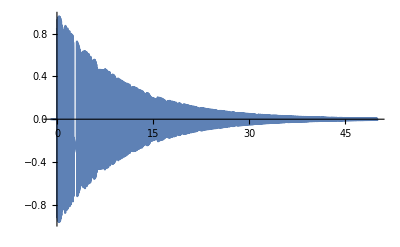

```mathematica
Plot[s[t], {t,-1, 50}, PlotRange->Full]
```

### A) Continuous Fourier Transform

```mathematica
Subscript[s, ft][ω_]= FourierTransform[s[t],t,ω]
```

(1000 √(2 π))/(1+40000 π^2-20 ⅈ ω-100 ω^2)

### B) Sample and estimation of aliases for the given frequencies

```mathematica
(* Reconstruction of transformed from samples*)
Subscript[s, ft-rec][ω_,T_] := (HeavisideTheta[ω+Pi/T]-HeavisideTheta[ω-Pi/T])  Sum[ Subscript[s, ft][ω + n(2Pi)/T], {n, -200, +200} ];
```

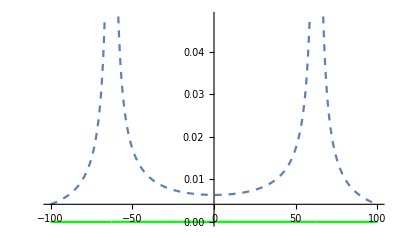

2.34838

```mathematica
(* 20 Hz *)
Show[ {Plot[  Abs[Subscript[s, ft][ω]],                                 {ω, -100, +100}, PlotStyle->Dashed  ],
          Plot[  Abs[Subscript[s, ft-rec][ω,1/Subscript[ν, s][[1]]] ],{ω, -100, +100} , PlotStyle->Green]}, PlotRange->All]

(* reconstruction error at 20 Hz *)
N[Sum[  (Abs[Subscript[s, ft][ω]]-Abs[Subscript[s, ft-rec][ω,1/Subscript[ν, s][[1]]] ])^2 , {ω, -100, +100} ] , 6]
```

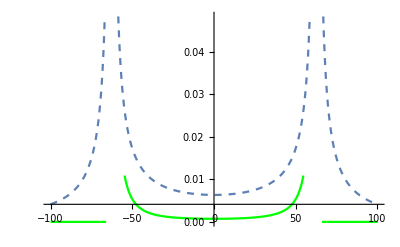

0.0487401

```mathematica
(* 21 Hz *)
Show[ {Plot[  Abs[Subscript[s, ft][ω]],                                 {ω, -100, +100}, PlotStyle->Dashed  ],
          Plot[  Abs[Subscript[s, ft-rec][ω,1/Subscript[ν, s][[2]]] ],{ω, -100, +100} , PlotStyle->Green]}, PlotRange->All]

(* reconstruction error at 21 Hz *)
N[Sum[  (Abs[Subscript[s, ft][ω]]-Abs[Subscript[s, ft-rec][ω,1/Subscript[ν, s][[2]]] ])^2 , {ω, -100, +100} ] , 6]
```

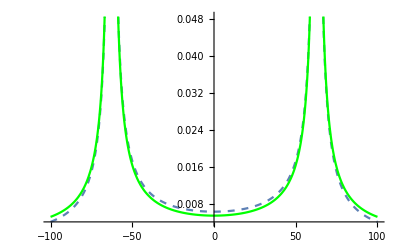

0.000173487

```mathematica
(* 50 Hz *)
Show[ {Plot[  Abs[Subscript[s, ft][ω]],                                 {ω, -100, +100}, PlotStyle->Dashed  ],
          Plot[  Abs[Subscript[s, ft-rec][ω,1/Subscript[ν, s][[3]]] ],{ω, -100, +100} , PlotStyle->Green]}, PlotRange->All]

(* reconstruction error at 50 Hz *)
N[Sum[  (Abs[Subscript[s, ft][ω]]-Abs[Subscript[s, ft-rec][ω,1/Subscript[ν, s][[3]]] ])^2 , {ω, -100, +100} ] , 6]
```

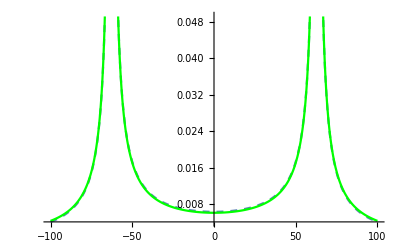

9.12534×10^-6

```mathematica
(* 100 Hz *)
Show[ {Plot[  Abs[Subscript[s, ft][ω]],                                 {ω, -100, +100}, PlotStyle->Dashed  ],
          Plot[  Abs[Subscript[s, ft-rec][ω,1/Subscript[ν, s][[4]]] ],{ω, -100, +100} , PlotStyle->Green]}, PlotRange->All]

(* reconstruction error at 100 Hz *)
N[Sum[  (Abs[Subscript[s, ft][ω]]-Abs[Subscript[s, ft-rec][ω,1/Subscript[ν, s][[4]]] ])^2 , {ω, -100, +100} ] , 6]
```

### Error estimation withing given ranges

```mathematica
(* Reconstruction of the non-trasformed signal from samples *)
Subscript[s, rec][t_, samples_, T_] := Sum[ samples[[k]] Sinc[Pi/T(t-k T)], {k, 1, Length@samples} ];
```

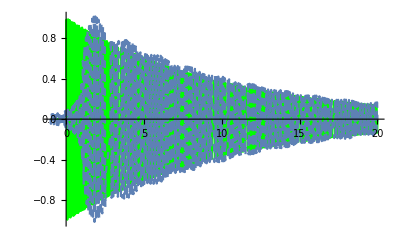

0.0990253

```mathematica
(* Subscript[v, s]=21 *)
points = Range[-1, 20, 1/Subscript[ν, s][[2]] ];
samples = Map[s, points];
Show[ {Plot[  s[t],                                                       {t, -1, 20}, PlotStyle->Green  ],
          Plot[  Subscript[s, rec][t, samples, 1/Subscript[ν, s][[2]]], {t, -1, 20}, PlotStyle->Dashed]}, PlotRange->All]
N[Sum[  (s[t]-Subscript[s, rec][t, samples, 1/Subscript[ν, s][[2]]])^2 , {t, -1, 20} ] , 6]
```

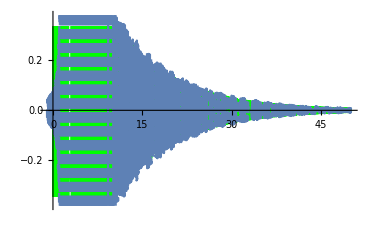

0.101286

```mathematica
points = Range[-1, 50, 1/Subscript[ν, s][[2]] ];
samples = Map[s, points];
Show[ {Plot[  s[t],                                                       {t, -1, 50}, PlotStyle->Green  ],
          Plot[  Subscript[s, rec][t, samples, 1/Subscript[ν, s][[2]]], {t, -1, 50}, PlotStyle->Dashed]}, PlotRange->All]
N[Sum[  (s[t]-Subscript[s, rec][t, samples, 1/Subscript[ν, s][[2]]])^2 , {t, -1, 50} ] , 6]
```

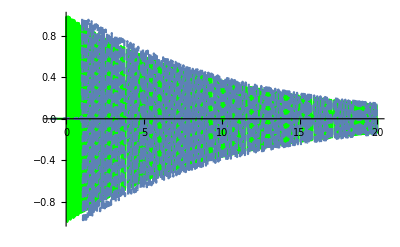

1.52861

```mathematica
(* Subscript[v, s]=100 *)
points = Range[-1, 20, 1/Subscript[ν, s][[4]] ];
samples = Map[s, points];
Show[ {Plot[  s[t],                                                       {t, -1, 20}, PlotStyle->Green  ],
          Plot[  Subscript[s, rec][t, samples, 1/Subscript[ν, s][[4]]], {t, -1, 20}, PlotStyle->Dashed]}, PlotRange->All]
N[Sum[  (s[t]-Subscript[s, rec][t, samples, 1/Subscript[ν, s][[4]]])^2 , {t, -1, 20} ] , 6]
```

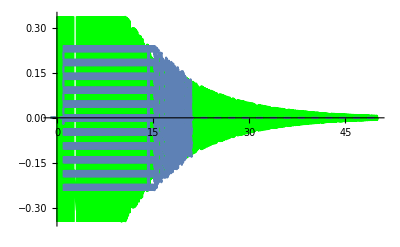

1.53495

```mathematica
points = Range[-1, 20, 1/Subscript[ν, s][[4]] ];
samples = Map[s, points];
Show[ {Plot[  s[t],                                                       {t, -1, 50}, PlotStyle->Green  ],
          Plot[  Subscript[s, rec][t, samples, 1/Subscript[ν, s][[4]]], {t, -1, 50}, PlotStyle->Dashed]}, PlotRange->All]
N[Sum[  (s[t]-Subscript[s, rec][t, samples, 1/Subscript[ν, s][[4]]])^2 , {t, -1, 50} ] , 6]
```